```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
mesh0=import@"crs_uniform.ntn";
mesh1=import@"mesh1.ntr";
```

```mathematica
highlight[mesh1,{"nodesNumn"},0]
```

-Graphics-

```mathematica
P0=Import@"P0.rua";
```

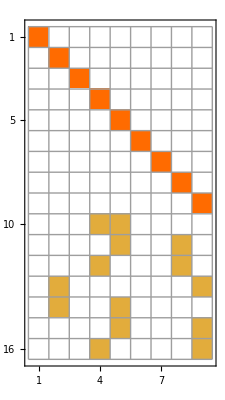

```mathematica
MatrixPlot[Transpose@P0,Mesh->All]
```